```mathematica
datadir=StringJoin[StringDelete[NotebookDirectory[],"/Mathematica"],"data/"]
```

## Random features

```mathematica
HP[psi_,phi_,eta_,zeta_,z_,P_]:=(
t=1/(z psi);
Pphi=1+(P-1)phi;
Ppsi=1+(P-1)psi;
A=Pphi Ppsi t zeta;
eq=P - 1-(eta-zeta) Ppsi Pphi t - A/(1-A);
Return[eq];
);
HG[psi_,phi_,eta_,zeta_,z_,G_]:=(
t=1/(z psi);
Pphi=1+(phi/psi)(z G-1);
Ppsi=z G;
A=Pphi Ppsi t zeta;
G-1/z- (psi/z)((eta-zeta) Ppsi Pphi t + A/(1-A) )
)
Options[rfResolvent]:={"psi"->1,"phi"->1,"eta"->1/2,"zeta"->1.4,"startr"->1,"starti"->1};
rfResolvent[lambda_,OptionsPattern[]]:=Module[{psi=OptionValue["psi"], phi=OptionValue["phi"],
 eta=OptionValue["eta"], zeta=OptionValue["zeta"],startr=OptionValue["startr"],starti=OptionValue["starti"],
z,sol,g, P, Pphi,  Ppsi,err},
z=lambda+(10^-10)I;
s=sr+I si;
sol=Quiet[FindRoot[{Re[HP[psi,phi,eta,zeta,z,s]],Im[HP[psi,phi,eta,zeta,z,s]]},{sr,startr},{si,starti}]];
g=sr+I si /.sol;
P=sr+I si /.sol; g=((psi P+1-psi) /z );
(*err=Abs[HG[psi,phi,eta,zeta,z,g]];*)
Return[g];
]
```

## Plotting

```mathematica
lists={};
eta=.39; zeta=.36;
phis={1/100,1/10,0.2,1,10,10};
legs=StringJoin["N/D=",ToString[N[#^-1]]]&/@phis;
lambdas=N@Subdivide[-3,2,500];
Do[
densities={phi};
gr=1; gi=1;
Do[
{g=rfResolvent[10^lambda, "psi"->0.1,"phi"->phi,"eta"-> eta,"zeta"->zeta, "startr"->gr,"starti"->gi];
(*Print[g];*)
gr=Re[g]; gi=Abs[Im[g]];
AppendTo[densities,{lambda,gi/Pi}];
},
{lambda,lambdas}
];
AppendTo[lists,densities],
{phi,phis}]

data=ExportString[lists,"RawJSON","Compact"->True];
title=
StringJoin[datadir,"spectrum_",ToString[zeta/eta],".json"];
Export[title,lists];
```

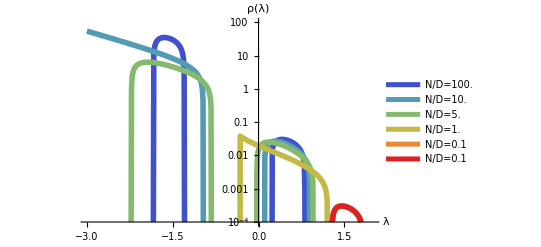

```mathematica
cmap=ColorData["Rainbow"];
colors={cmap[#],Thickness[0.01]}&/@(Range[Length[phis]]/Length[phis]);
style={FontSize->14,FontColor->Black};
plot=ListLogPlot[lists[[;;,2;;-1]],PlotRange->{10^-4,100}, PlotLegends->legs,PlotStyle->colors,Joined->True,LabelStyle->style,AxesLabel->{"λ","ρ(λ)"}]
```